```mathematica
(*Load the finite element package*)Needs["NDSolve`FEM`"];

(*Define parameters*)
omega=1;  (*Replace with your desired value*)
r=1;      (*Replace with your desired value*)
xMax=12;   (*Set the maximum x value*)
zMax=22;   (*Set the maximum z value*)
LD = 1/omega

(*Define the computational domain*)
region=Rectangle[{-xMax,0},{xMax,zMax}];

(*Define the PDE with NeumannValue terms included*)
pde=-Laplacian[C[x,z],{x,z}]+NeumannValue[omega*C[x,z]-r*UnitStep[-x],z==0]+NeumannValue[0,x==-xMax||x==xMax||z==zMax]==0;

(*Increase spatial resolution by refining the mesh*)
meshOptions={"MaxCellMeasure"->0.001};  (*Further decrease for finer mesh*)

(*Define the Analytical Solution for C(x,0)*)
CAnalytical[x_]:=Module[{nMax=50,sum=0,kn},
sum=Sum[Module[{knLocal=Pi (2 n+1)/(2 xMax),(*k_n definition*)numerator,denominator},
numerator=Sin[knLocal x] Cosh[knLocal zMax];
denominator=knLocal (knLocal Sinh[knLocal zMax]+omega Cosh[knLocal zMax]);
numerator/denominator],{n,0,nMax}];
(r/(2 omega))-(r/xMax) sum];

CAnalyticApprox[x_]:= (r/omega)*(HeavisideTheta[-x]+(Cos[x/LD]/π) Sign[x] (π/2-SinIntegral[ Abs[x]/LD])+(Sin[x/LD]/π) CosIntegral[Abs[x]/LD])

CAnalyticlFF[x_]:= (r/omega) * (HeavisideTheta[-x]+ LD/π/x)

CAnalyticlNF[x_]:=(r/(Pi*omega))*(HeavisideTheta[-x] + Sign[x]*(Pi/2-(x/LD))+(x/LD)*(Log[Abs[x]/LD]+EulerGamma))
```

1

```mathematica
(*Solve the PDE*)
solution=NDSolveValue[pde,C,{x,z}∈region,Method->{"FiniteElement","MeshOptions"->meshOptions}];
```

```mathematica
plot1D = 
 Plot[
 {
 solution[x, 0] - 0.001, 
 CAnalytical[x] + 0.001, 
 CAnalyticApprox[x], 
 If[7 <= x <= xMax, CAnalyticlFF[x] + 0.005, Undefined],
 If[0.0001 <= x <= 0.35, CAnalyticlNF[x] + 0.005, Undefined] 
 }, 
  {x, -xMax, xMax}, 
  PlotRange -> All, 
  FrameLabel -> {Style["x", FontFamily -> "Helvetica Neue", 
     FontSize -> 22, FontColor -> Black], 
    Style["C(x,0)", FontFamily -> "Helvetica Neue", FontSize -> 22, 
     FontColor -> Black]}, 
  PlotStyle -> {
    {Thick, Black, Dashing[Medium]},  (* Numerical: Black, Thick *)
    {Thick, Red, Dashing[Medium]},    (* Analytical: Red, Thick *)
    {Thick, Blue, Dashing[Medium]},   (* Approx. Analytical: Blue, Thick *)
    {Thick, Purple, Dashing[Medium]},          (* CAnalyticlFF: Purple, Dotted *)
    {Thick, Green, Dashing[Medium]}         (* CAnalyticlNF: Green, Dot-Dashed *)
    }, 
  PlotLegends -> 
   Placed[
    LineLegend[
     {Directive[Thick, Black, Dashing[Medium]], 
      Directive[Thick, Red, Dashing[Medium]], 
      Directive[Thick, Blue, Dashing[Medium]], 
      Directive[Thick, Purple, Dashing[Medium]], 
      Directive[Thick, Green, Dashing[Medium]]}, 
     {"Numerical Solution", 
     "Eq. S11", 
     "Eq. S12", 
     "Eq. S13", 
     "Eq. S14"}, 
     LabelStyle -> {FontFamily -> "Helvetica Neue", FontSize -> 14}, 
     LegendMarkerSize -> {40, 3}], {0.8, 0.85}], 
  GridLines -> Automatic, 
  ImageSize -> 800, 
  BaseStyle -> {FontFamily -> "Helvetica Neue", FontSize -> 14}, 
  Frame -> True, 
  FrameStyle -> 
   Directive[GrayLevel[0], 13, FontFamily -> "Helvetica Neue", 
    AbsoluteThickness[1.0']], 
  FrameTicks -> Automatic];
```

```mathematica
(*3D Plot of the solution with higher spatial resolution and a color bar*)
plot3D=Plot3D[solution[x,z],{x,-xMax,xMax},{z,0,zMax},PlotRange->All,AxesLabel->{Style["x",FontFamily->"Helvetica Neue",FontSize->16,FontWeight->Bold],Style["z",FontFamily->"Helvetica Neue",FontSize->16,FontWeight->Bold],Style["C(x, z)",FontFamily->"Helvetica Neue",FontSize->16,FontWeight->Bold]},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->None,PlotLegends->Placed[BarLegend["Rainbow",LegendLabel->Style["C(x, z)",FontFamily->"Helvetica Neue",FontSize->14,Bold],LabelStyle->{FontFamily->"Helvetica Neue",FontSize->16}],Scaled[{1.05,0.5}] (*Positioning the color bar next to the 3D plot*)],PlotPoints->100,(*Increased initial sampling points*)MaxRecursion->6,(*Increased adaptive refinement*)PerformanceGoal->"Quality",ImageSize->800,(*Increased Image Size for Higher Resolution*)LabelStyle->{FontFamily->"Helvetica Neue",FontSize->16},(*Font size for tick labels*)BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}   (*Base font size*)];
```

```mathematica
plot3D
```

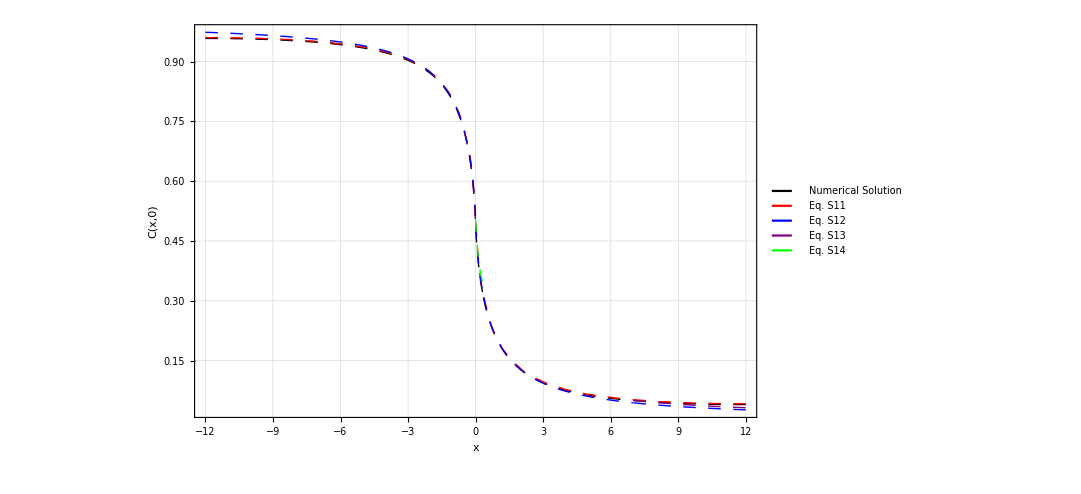

```mathematica
plot1D
```

```mathematica
Export["1dplot.png", plot1D, ImageResolution->800]
```

1dplot.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1dplot.png"]]]
```